InterpolatingFunction::dmval: Input value {0.100064,-0.035694} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
Hdgza[x_,t_]=x*aHdgzall[x,-t];
Hera[x_,t_]=x*aHerall[x,-t];
Hdgfa[x_,t_]=x*aHdgfall[x,-t];
Edgza[x_,t_]=x*aEdgzall[x,-t];
Eera[x_,t_]=x*aEerall[x,-t];
Edgfa[x_,t_]=x*aEdgfall[x,-t];
```

```mathematica
Hdgzm[x_,t_]=x*mHdgzall[x,-t];
Herm[x_,t_]=x*mHerall[x,-t];
Hdgfm[x_,t_]=x*mHdgfall[x,-t];
Edgzm[x_,t_]=x*mEdgzall[x,-t];
Eerm[x_,t_]=x*mEerall[x,-t];
Edgfm[x_,t_]=x*mEdgfall[x,-t];
```

```mathematica
Herk[x_,t_]=x*kpHall[x,-t];
Eerl[x_,t_]=x*lpEall[x,-t];
```

```mathematica
(*图agpd*)
```

```mathematica
pHa=Show[Plot3D[Hdgza[x,t],{x,0.1,1},{t,0.03562509090909091,1},PlotRange->All],Plot3D[Hdgfa[x,t],{x,-1,-0.1},{t,0.03562509090909091,1},PlotRange->All],Plot3D[Hera[x,t],{x,-0.1,0.1},{t,0.03562509090909091,1},PlotRange->All],AxesLabel->{"x","-t(GeV^2)","(xH^u)_oct(x,ξ,t)"},LabelStyle->Directive[Black,Thick,12]]
```

InterpolatingFunction::dmval: Input value {0.100064,-0.035694} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.999936,-0.035694} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0999857,-0.035694} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
pEa=Show[Plot3D[Edgza[x,t],{x,0.1,1},{t,0.03562509090909091,1},PlotRange->All],Plot3D[Edgfa[x,t],{x,-1,-0.1},{t,0.03562509090909091,1},PlotRange->All],Plot3D[Eera[x,t],{x,-0.1,0.1},{t,0.03562509090909091,1},PlotRange->All],AxesLabel->{"x","-t(GeV^2)","(xE^u)_oct(x,ξ,t)"},LabelStyle->Directive[Black,Thick,12]]
```

InterpolatingFunction::dmval: Input value {0.100064,-0.035694} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.999936,-0.035694} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0999857,-0.035694} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
StyleBox[SubscriptBox["xH^u","oct"],FontSlant->Italic]//DisplayForm
```

(xH^u)_oct

```mathematica
pHm=Show[Plot3D[Hdgzm[x,t],{x,0.1,1},{t,0.03562509090909091,1},PlotRange->All],Plot3D[Hdgfm[x,t],{x,-1,-0.1},{t,0.03562509090909091,1},PlotRange->All],Plot3D[Herm[x,t],{x,-0.1,0.1},{t,0.03562509090909091,1},PlotRange->All],AxesLabel->{"x","-t(GeV^2)","(xH^u)_dec(x,ξ,t)"},LabelStyle->Directive[Black,Thick,12]]
pEm=Show[Plot3D[Edgzm[x,t],{x,0.1,1},{t,0.03562509090909091,1},PlotRange->All],Plot3D[Edgfm[x,t],{x,-1,-0.1},{t,0.03562509090909091,1},PlotRange->All],Plot3D[Eerm[x,t],{x,-0.1,0.1},{t,0.03562509090909091,1},PlotRange->All],AxesLabel->{"x","-t(GeV^2)","(xE^u)_dec(x,ξ,t)"},LabelStyle->Directive[Black,Thick,12]]
```

InterpolatingFunction::dmval: Input value {0.100064,-0.035694} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.999936,-0.035694} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0999857,-0.035694} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

InterpolatingFunction::dmval: Input value {0.100064,-0.035694} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.108036,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.112054,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
pHk=Show[Plot3D[Herk[x,t],{x,-0.1,0.1},{t,0.03562509090909091,1},PlotRange->All],AxesLabel->{"x","-t(GeV^2)","(xH^u)_bub(x,ξ,t)"},LabelStyle->Directive[Black,Thick,12]]
pEl=Show[Plot3D[Eerl[x,t],{x,-0.1,0.1},{t,0.03562509090909091,1},PlotRange->All],AxesLabel->{"x","-t(GeV^2)","(xE^u)_bub(x,ξ,t)"},LabelStyle->Directive[Black,Thick,12]]
```

InterpolatingFunction::dmval: Input value {-0.0999857,-0.035694} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics3D-

InterpolatingFunction::dmval: Input value {-0.0999857,-0.035694} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics3D-

```mathematica
pathHa=FileNameJoin[{"G:\\calc-online\\gpd\\3dre",
"Hua3d-0.1.pdf"}];
pathEa=FileNameJoin[{"G:\\calc-online\\gpd\\3dre",
"Eua3d-0.1.pdf"}];
pathHm=FileNameJoin[{"G:\\calc-online\\gpd\\3dre",
"Hum3d-0.1.pdf"}];
pathEm=FileNameJoin[{"G:\\calc-online\\gpd\\3dre",
"Eum3d-0.1.pdf"}];
pathHk=FileNameJoin[{"G:\\calc-online\\gpd\\3dre",
"Huk3d-0.1.pdf"}];
pathEl=FileNameJoin[{"G:\\calc-online\\gpd\\3dre",
"Eul3d-0.1.pdf"}];
```

```mathematica
Export[pathHa,pHa]
Export[pathEa,pEa]
Export[pathHm,pHm]
Export[pathEm,pEm]
Export[pathHk,pHk]
Export[pathEl,pEl]
```

G:\calc-online\gpd\3dre\Hua3d-0.1.pdf

G:\calc-online\gpd\3dre\Eua3d-0.1.pdf

G:\calc-online\gpd\3dre\Hum3d-0.1.pdf

G:\calc-online\gpd\3dre\Eum3d-0.1.pdf

G:\calc-online\gpd\3dre\Huk3d-0.1.pdf

G:\calc-online\gpd\3dre\Eul3d-0.1.pdf

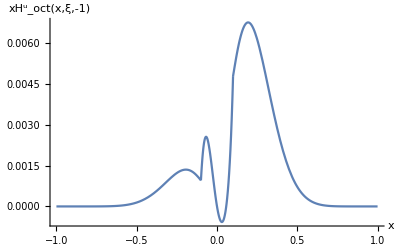

```mathematica
pHa1=Show[Plot[Hdgza[x,1],{x,0.1,1},PlotRange->All],Plot[Hdgfa[x,1],{x,-1,-0.1},PlotRange->All],Plot[Hera[x,1],{x,-0.1,0.1},PlotRange->All],AxesLabel->{"x","(xH^u)_oct(x,ξ,-1)"},LabelStyle->Directive[Black,Thick,12]]
```

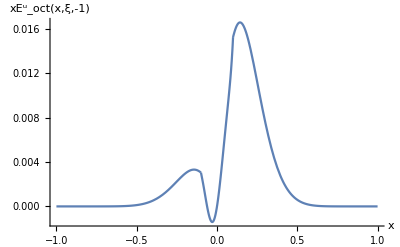

```mathematica
pEa1=Show[Plot[Edgza[x,1],{x,0.1,1},PlotRange->All],Plot[Edgfa[x,1],{x,-1,-0.1},PlotRange->All],Plot[Eera[x,1],{x,-0.1,0.1},PlotRange->All],AxesLabel->{"x","(xE^u)_oct(x,ξ,-1)"},LabelStyle->Directive[Black,Thick,12]]
```

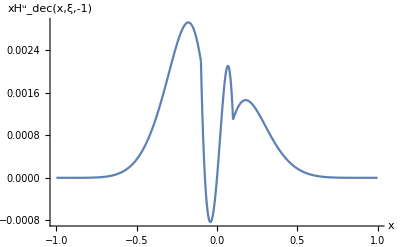

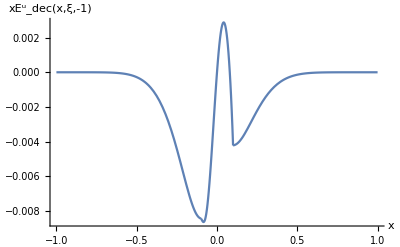

```mathematica
pHm1=Show[Plot[Hdgzm[x,1],{x,0.1,1},PlotRange->All],Plot[Hdgfm[x,1],{x,-1,-0.1},PlotRange->All],Plot[Herm[x,1],{x,-0.1,0.1},PlotRange->All],AxesLabel->{"x","(xH^u)_dec(x,ξ,-1)"},LabelStyle->Directive[Black,Thick,12]]
pEm1=Show[Plot[Edgzm[x,1],{x,0.1,1},PlotRange->All],Plot[Edgfm[x,1],{x,-1,-0.1},PlotRange->All],Plot[Eerm[x,1],{x,-0.1,0.1},PlotRange->All],AxesLabel->{"x","(xE^u)_dec(x,ξ,-1)"},LabelStyle->Directive[Black,Thick,12]]
```

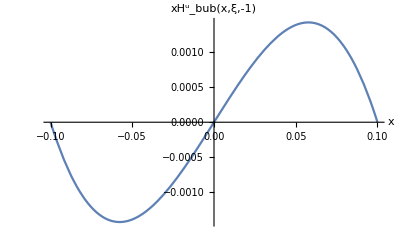

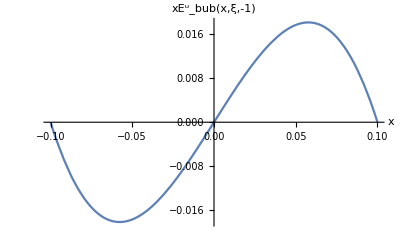

```mathematica
pHk1=Show[Plot[Herk[x,1],{x,-0.1,0.1},PlotRange->All],AxesLabel->{"x","(xH^u)_bub(x,ξ,-1)"},LabelStyle->Directive[Black,Thick,12]]
pEl1=Show[Plot[Eerl[x,1],{x,-0.1,0.1},PlotRange->All],AxesLabel->{"x","(xE^u)_bub(x,ξ,-1)"},LabelStyle->Directive[Black,Thick,12]]
```

```mathematica
Eerl[0.06,1]
```

0.018127

```mathematica
pathHa1=FileNameJoin[{"G:\\calc-online\\gpd\\3dre",
"Hua2d-0.1.pdf"}];
pathEa1=FileNameJoin[{"G:\\calc-online\\gpd\\3dre",
"Eua2d-0.1.pdf"}];
pathHm1=FileNameJoin[{"G:\\calc-online\\gpd\\3dre",
"Hum2d-0.1.pdf"}];
pathEm1=FileNameJoin[{"G:\\calc-online\\gpd\\3dre",
"Eum2d-0.1.pdf"}];
pathHk1=FileNameJoin[{"G:\\calc-online\\gpd\\3dre",
"Huk2d-0.1.pdf"}];
pathEl1=FileNameJoin[{"G:\\calc-online\\gpd\\3dre",
"Eul2d-0.1.pdf"}];
```

```mathematica
Export[pathHa1,pHa1]
Export[pathEa1,pEa1]
Export[pathHm1,pHm1]
Export[pathEm1,pEm1]
Export[pathHk1,pHk1]
Export[pathEl1,pEl1]
```

G:\calc-online\gpd\3dre\Hua2d-0.1.pdf

G:\calc-online\gpd\3dre\Eua2d-0.1.pdf

G:\calc-online\gpd\3dre\Hum2d-0.1.pdf

G:\calc-online\gpd\3dre\Eum2d-0.1.pdf

G:\calc-online\gpd\3dre\Huk2d-0.1.pdf

G:\calc-online\gpd\3dre\Eul2d-0.1.pdf

```mathematica
NIntegrate[aHdgzall[x,-1],{x,0.1,1}]+NIntegrate[aHerall[x,-1],{x,-0.1,0.1}]+NIntegrate[aHdgfall[x,-1],{x,-1,-0.1}]
```

0.00256054+0. ⅈ

```mathematica
(*师兄结果*)0.00277
```